```mathematica
area1prop = RandomVariate[BinomialDistribution[100, 0.5], 10000]/100;
```

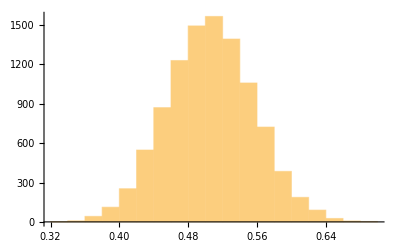

```mathematica
Histogram[area1prop]
```

```mathematica
area2prop = RandomVariate[BinomialDistribution[100, 0.5], 10000]/100;
```

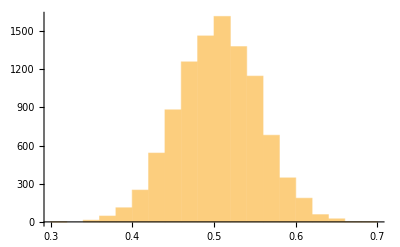

```mathematica
Histogram[area2prop]
```

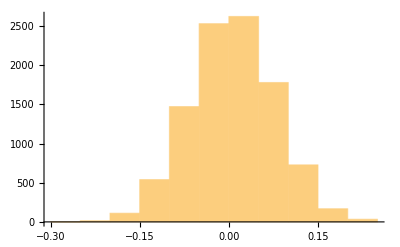

```mathematica
Histogram[area1prop - area2prop]
```

```mathematica
difference  = area1prop - area2prop;
```

```mathematica
FindDistribution[difference]
```

NormalDistribution[0.000111828,0.0912004]

```mathematica
Probability[x≥0.200, x\[Distributed]NormalDistribution[0.001857827848347659,0.09195905241852936]]
```

0.0155935

```mathematica
Probability[(x≥0.15)||(x≤-0.15), x\[Distributed]NormalDistribution[0.001857827848347659,0.07195905241852936]]
```

0.0371761

```mathematica
Probability[(x≥0.15)||(x≤-0.15), x\[Distributed]NormalDistribution[0,0.07 ]]
```

0.0321246

```mathematica
(0.5*0.5)*(1/50)
```

0.005

```mathematica
Sqrt[0.005]
```

0.0707107

```mathematica
Probability[(x≥0.15)||(x≤-0.15), x\[Distributed]NormalDistribution[0,0.07071067811865475]]
```

0.0338949

https://online.stat.psu.edu/stat415/lesson/9/9.4

```mathematica
2+2
```

4